```mathematica
scan=ReadList["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Vacuum_Labs/5_sem/Atomic\ power\ microscope/20.11.2018/scan1_pure.txt",Number,WordSeparators->{"\t", " "}];
```

```mathematica
scan=ArrayReshape[scan,{200,200}];
```

```mathematica
ListPlot3D[scan, PlotTheme->"Minimal"]
```

-Graphics3D-

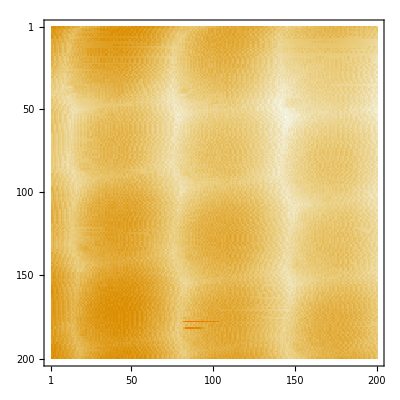

```mathematica
MatrixPlot[scan]
```